# Vaje iz Mathematice

Rešuj naloge v celicah med navodili. Pomagaj si z gradivom na spletni učilnici in z vgrajeno pomočjo.

1. naloga: Dokaži, da za poljubni 2×2 matriki A in B velja enakost (AB)^-1 = B^-1 A^-1.

```mathematica
A={{a1, a2}, {a3, a4}};
B={{b1, b2}, {b3, b4}};
Simplify[Inverse[A.B]==Inverse[B].Inverse[A]]
```

True

2. naloga: Določi vsa realna števila, ki zadoščajo neenačbi (| x-3 |)/(x+1) > √(3-2x)

```mathematica
Reduce[Abs[x-3]/(x+1) >√(3-2x),x, Reals]
```

-1<x<1||1<x≤3/2

3. naloga: Poišči vse delitelje števila 16524000.

```mathematica
Divisors[16524000]
```

{1,2,3,4,5,6,8,9,10,12,15,16,17,18,20,24,25,27,30,32,34,36,40,45,48,50,51,54,60,68,72,75,80,81,85,90,96,100,102,108,120,125,135,136,144,150,153,160,162,170,180,200,204,216,225,240,243,250,255,270,272,288,300,306,324,340,360,375,400,405,408,425,432,450,459,480,486,500,510,540,544,600,612,648,675,680,720,750,765,800,810,816,850,864,900,918,972,1000,1020,1080,1125,1200,1215,1224,1275,1296,1350,1360,1377,1440,1500,1530,1620,1632,1700,1800,1836,1944,2000,2025,2040,2125,2160,2250,2295,2400,2430,2448,2550,2592,2700,2720,2754,3000,3060,3240,3375,3400,3600,3672,3825,3888,4000,4050,4080,4131,4250,4320,4500,4590,4860,4896,5100,5400,5508,6000,6075,6120,6375,6480,6750,6800,6885,7200,7344,7650,7776,8100,8160,8262,8500,9000,9180,9720,10125,10200,10800,11016,11475,12000,12150,12240,12750,12960,13500,13600,13770,14688,15300,16200,16524,17000,18000,18360,19125,19440,20250,20400,20655,21600,22032,22950,24300,24480,25500,27000,27540,30375,30600,32400,33048,34000,34425,36000,36720,38250,38880,40500,40800,41310,44064,45900,48600,51000,54000,55080,57375,60750,61200,64800,66096,68000,68850,73440,76500,81000,82620,91800,97200,102000,103275,108000,110160,114750,121500,122400,132192,137700,153000,162000,165240,172125,183600,194400,204000,206550,220320,229500,243000,275400,306000,324000,330480,344250,367200,413100,459000,486000,516375,550800,612000,660960,688500,826200,918000,972000,1032750,1101600,1377000,1652400,1836000,2065500,2754000,3304800,4131000,5508000,8262000,16524000}

Katera od njih so praštevila?

```mathematica
Select[Divisors[16524000],PrimeQ]
```

{2,3,5,17}

S kakšnimi potencami nastopajo v razcepu števila 16524000?

```mathematica
FactorInteger[16524000]
```

{{2,5},{3,5},{5,3},{17,1}}

4. naloga: V vgrajeni pomoči si oglej, kako se uporablja ukaz Manipulate. Nato nariši graf funkcije y = a sin(k x + n), pri čemer boš lahko vrednosti parametrov a, k in n spreminjal v obsegu od -3 do 3. Območje risanja omeji na [-5,5] × [-5,5]. Enoti na x in y osi naj bosta enako veliki.

```mathematica
Manipulate[Plot[a*Sin[k*x+n],{x,-5,5},PlotRange->{-5,5}],{a,-3,3},{k,-3,3},{n,-3,3}]
```

5. naloga: Nariši graf premice y = k x + n in na isti sliki še pravokotnico nanjo, ki gre skozi točko T(x_0, y_0). Pomagaj si z ukazom Manipulate, da boš lahko spreminjal vrednosti parametrov k, n, x_0 in y_0. Na sliki označi z majhnim krogcem, kje leži točka T.

```mathematica
Manipulate[Plot[{k*x+n,-1/k*(x-x0)+y0,p},{x,-5,5},PlotRange->{-5,5},AspectRatio->Automatic,Epilog->Disk[{x0,y0},0.1]],{k,-2,2},{n,-2,2},{y0,-3,3},{x0,-3,3}]
```

6. naloga: Definiraj funkcijo f(x) = (x(x-2))^2/(x^2+1) ter nariši njen graf skupaj s tangento v točki x_0.  Pomagaj si z ukazom Manipulate, da boš lahko spreminjal vrednost parametra x_0. Na sliki označi z majhnim krogcem, kje se tangenta dotika grafa funkcije.

```mathematica
funkcija[x_]:=(x(x-2)^2)/(x^2+1)
Manipulate[Plot[{funkcija[x],funkcija[x0]+funkcija'[x0]*(x-x0)},{x,-10,10},PlotRange->{-10,10},AspectRatio->Automatic,Epilog->Disk[{x0,funkcija[x0]},0.2]],{x0,-5,5}]
```

7. naloga: Definiraj funkcijo g(x) = -x^3 + 8 in nariši njen graf nad intervalom [-3,3].

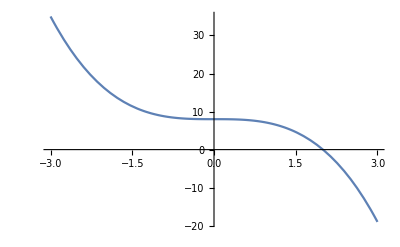

```mathematica
g[x_]:=-x^3+8
Plot[g[x],{x,-3,3}]
```

Izračunaj ploščino lika, ki ga (v prvem kvadrantu) omejujeta koordinatni osi in graf te funkcije.

```mathematica
tocka=Solve[g[x]==0,x,Reals]
Integrate[g[x],{x,0,2}]
```

{{x→2}}

12

Še enkrat nariši graf funkcije g nad istim intervalom, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.

8. naloga: Definiraj funkciji h(x) = x^2-8 in k(x) = -x^2+10 ter nariši njuna grafa.poišči njuni presečišči. Nato izračunaj še ploščino lika, ki ga omejujeta grafa teh dveh funkcij.

Izračunaj ploščino lika, ki ga omejujeta grafa teh dveh funkcij.

Še enkrat nariši grafa obeh funkcij, le da bo tokrat območje, katerega ploščino si izračunal, pobarvano.